```mathematica
link=Install[LinkConnect["45345@192.168.150.130,40925@192.168.150.130",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle=With[{mmin=50,mmax=1000,
ϵ=1./(16*1836.),ωeOΩe=1.2,Ωc=1.,
ηr={0.0002,0.001,0.001,0.0014,0.0013,0.0028,0.0037,0.0046,0.0046,0.0037,0.0027,0.0014,0.0014,0.001,0.001,0.0002},
vrr={0.2171,0.3636,0.5022,0.6404,0.7656,0.8059,0.8264,0.8513,0.8513,0.8264,0.7637,0.7656,0.6404,0.5022,0.3445,0.2059},
vrd={0.9844,0.9398,0.8103,0.7030,0.5778,0.4012,0.2355,0.0785,-0.0785,-0.2355,-0.3802,-0.5778,-0.7030,-0.8103,-0.8906,-0.9329},
vthj ={0.326,0.2795,0.2795,0.2562,0.2562,0.2329,0.2329,0.1863,0.1863,0.2329,0.2329,0.2562,0.2562,0.2795,0.2795,0.326}*0.3
},
Module[{
ηs={0.864,0.0232,0.006,0.0606,0.0142,Sequence@@ηr,1.},
θs={0.032,0.19,0.1,0.06,0.21,Sequence@@vthj,0.1*√(1/ϵ)},
Ωcs,ωps2,θ1s,θ2s,vrs,vds,c
}, c=ωeOΩe/√ϵ;
Ωcs={16,16,4,1,1,Sequence@@ConstantArray[1,Length[ηr]],-1/ϵ}Ωc//N;
ωps2=c^2 ηs{16,16,4,1,1,Sequence@@ConstantArray[1,Length[ηr]],1/ϵ}Ωc^2//N;
θ1s=θs;
θ2s=θs;
vrs={0,0,0,0,0,Sequence@@vrr,0}//N;
vds={0,0,0,0,0,Sequence@@vrd,0}//N;
(*distribution functions*)
dist=Thread[wstpDRingDistribution[Ωcs,Sqrt[ωps2],θs,θs,vds,vrs]];
wstpDCreateDispersionObject[c,dist]]];
```

```mathematica
handle//wstpDDescription
wstpDSetMinimumCyclotronOrder[handle,200]
```

N4Disp10DispersionE[c->205.673, jmin->5, jmax->2000, vdfs->{
	N4Disp17MaxwellianRingVDFE[Oc->16, op->(764.706,0), th1->0.032, th2->0.032, vd->0, vr->0],
	N4Disp17MaxwellianRingVDFE[Oc->16, op->(125.309,0), th1->0.19, th2->0.19, vd->0, vr->0],
	N4Disp17MaxwellianRingVDFE[Oc->4, op->(31.8627,0), th1->0.1, th2->0.1, vd->0, vr->0],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(50.6307,0), th1->0.06, th2->0.06, vd->0, vr->0],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(24.5088,0), th1->0.21, th2->0.21, vd->0, vr->0],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(2.90866,0), th1->0.0978, th2->0.0978, vd->0.9844, vr->0.2171],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(6.50396,0), th1->0.08385, th2->0.08385, vd->0.9398, vr->0.3636],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(6.50396,0), th1->0.08385, th2->0.08385, vd->0.8103, vr->0.5022],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(7.69558,0), th1->0.07686, th2->0.07686, vd->0.703, vr->0.6404],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(7.41565,0), th1->0.07686, th2->0.07686, vd->0.5778, vr->0.7656],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(10.8832,0), th1->0.06987, th2->0.06987, vd->0.4012, vr->0.8059],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(12.5106,0), th1->0.06987, th2->0.06987, vd->0.2355, vr->0.8264],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(13.9494,0), th1->0.05589, th2->0.05589, vd->0.0785, vr->0.8513],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(13.9494,0), th1->0.05589, th2->0.05589, vd->-0.0785, vr->0.8513],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(12.5106,0), th1->0.06987, th2->0.06987, vd->-0.2355, vr->0.8264],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(10.6871,0), th1->0.06987, th2->0.06987, vd->-0.3802, vr->0.7637],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(7.69558,0), th1->0.07686, th2->0.07686, vd->-0.5778, vr->0.7656],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(7.69558,0), th1->0.07686, th2->0.07686, vd->-0.703, vr->0.6404],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(6.50396,0), th1->0.08385, th2->0.08385, vd->-0.8103, vr->0.5022],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(6.50396,0), th1->0.08385, th2->0.08385, vd->-0.8906, vr->0.3445],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(2.90866,0), th1->0.0978, th2->0.0978, vd->-0.9329, vr->0.2059],
	N4Disp17MaxwellianRingVDFE[Oc->-29376, op->(35251.2,0), th1->17.1394, th2->17.1394, vd->0, vr->0]
}]

{200,2000}

```mathematica
With[{handle=handle,k1=0.55,k0=6.,ω0=2.9+0.1I},
"ω"/.wstpDFindRoot[handle,k1,k0,ω0 (1+0.01 I {0,1,2}),MaxIterations->10,"UpdateMinimumCyclotronOrderFromPreviousIteration"->False,"ReturnDispersionMatrix"->False]]
```

2.68013+0.0211183 ⅈ

```mathematica
check=With[{k1=0.6,k0=6.0},wstpDFindRoot[handle,k1,k0,Complex[2.9,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

{2.74301-0.0216825 ⅈ,2.73009-0.0215456 ⅈ,2.71716-0.0208854 ⅈ,2.70421-0.0194608 ⅈ,2.69132-0.0168145 ⅈ,2.67872-0.0119406 ⅈ,2.66804-0.00232774 ⅈ,2.66894+0.0142214 ⅈ,2.70575+0.032872 ⅈ,2.73886+0.0632278 ⅈ,2.77622+0.0789947 ⅈ}

{2.74301-0.0216825 ⅈ,2.73009-0.0215456 ⅈ,2.71716-0.0208854 ⅈ,2.70421-0.0194608 ⅈ,2.69132-0.0168145 ⅈ,2.67872-0.0119406 ⅈ,2.66804-0.00232774 ⅈ,2.66894+0.0142214 ⅈ,2.70575+0.032872 ⅈ,2.73886+0.0632278 ⅈ,2.77622+0.0789947 ⅈ,2.81725+0.0900338 ⅈ,2.85968+0.0961142 ⅈ,2.90373+0.0992069 ⅈ,2.94752+0.0981142 ⅈ,2.99506+0.092973 ⅈ,3.04272+0.089239 ⅈ,3.0888+0.0803256 ⅈ,3.1397+0.070778 ⅈ,3.18517+0.0618553 ⅈ,3.22984+0.0422141 ⅈ,3.28773+0.0310614 ⅈ,3.3241+0.0210747 ⅈ,3.34797+0.0042113 ⅈ,3.359-0.0128022 ⅈ,3.36522-0.0279163 ⅈ,3.373-0.043736 ⅈ,3.39059-0.0581491 ⅈ,3.40845-0.053572 ⅈ,3.41257-0.0502881 ⅈ,3.41434-0.0518841 ⅈ}

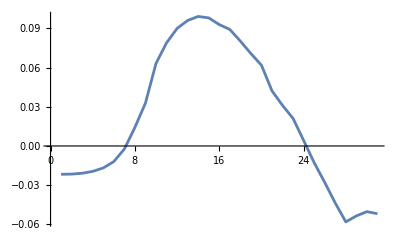

```mathematica
toleft=With[{k1=Range[0.6,0.4,-0.02]},wstpDFindRoot[handle,k1,ConstantArray[6.0,Length[k1]],Complex[2.9,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
toright=With[{k1=Range[0.62,1.0,0.02]},wstpDFindRoot[handle,k1,ConstantArray[6.0,Length[k1]],Complex[2.9,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
l=Reverse[toleft[[2,2]]]
total=Join[l,toright[[2,2]]]
ListLinePlot[Im[total]]
```

```mathematica
todown={};
With[{k1=Range[0.6,0.4,-0.02]},

Do[sol=wstpDFindRoot[handle,k1,ConstantArray[k0,Length[k1]],Complex[2.9,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100];
todown=Append[todown,Im[sol[[2,2]]]],
{k0,5.0,8.0,0.05}]];
toup={};
With[{k1=Range[0.62,1.0,0.02]},

Do[sol=wstpDFindRoot[handle,k1,ConstantArray[k0,Length[k1]],Complex[2.9,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100];
toup=Append[toup,Im[sol[[2,2]]]],
{k0,5.0,8.0,0.05}]];
```

```mathematica
todown
```

```mathematica
Reverse[todown]
```

{{0.00637062,0.0186658,0.0268689,0.0197242,0.00111535,-0.0151748,-0.0234695,-0.0272671,-0.0289241,-0.0416058,-0.0402505},{0.0107207,0.0198066,0.027252,0.0206378,0.00233093,-0.0139937,-0.0224339,-0.0264153,-0.0282164,-0.0288551,-0.0406664},{0.0152004,0.0210629,0.0276518,0.021522,0.00352557,-0.0128586,-0.0214486,-0.0255974,-0.0275323,-0.0282684,-0.0410792},{0.0195246,0.0223839,0.0280907,0.0223737,0.00469481,-0.0117667,-0.020513,-0.0248151,-0.0268745,-0.0277028,-0.0277797},{0.0236395,0.0237396,0.0285981,0.0231904,0.00583368,-0.0107167,-0.0196227,-0.0240699,-0.0262453,-0.0271603,-0.0273025},{0.0275518,0.0251215,0.0292076,0.0239706,0.0069368,-0.0097088,-0.0187784,-0.023363,-0.0256466,-0.0266432,-0.0268472},{0.0312815,0.0265446,0.0299511,0.0247143,0.00799829,-0.00874427,-0.0179802,-0.0226955,-0.0250803,-0.0261534,-0.0264155},{0.0348501,0.028053,0.03085,0.0254232,0.00901187,-0.00782552,-0.0172286,-0.0220688,-0.0245481,-0.0256901,-0.0260072},{0.0382774,0.0297298,0.0319077,0.0261018,0.00997085,-0.00695582,-0.016525,-0.02148,-0.0240488,-0.0252604,-0.0256284},{0.0415809,0.0317013,0.0331094,0.0267574,0.0108683,-0.00613979,-0.0158716,-0.0209444,-0.0235905,-0.0248635,-0.0252785},{0.044776,0.0341037,0.0344282,0.0274011,0.0116967,-0.00538252,-0.015271,-0.0204499,-0.0231719,-0.0245011,-0.0249591},{0.0478765,0.0369844,0.035834,0.0280488,0.0124483,-0.00469013,-0.0147266,-0.0200038,-0.0227948,-0.024175,-0.0246719},{0.0508945,0.0402318,0.0373004,0.0287198,0.0131154,-0.0040696,-0.0142422,-0.0196088,-0.0224615,-0.023887,-0.0244186},{0.0538405,0.0436526,0.0388082,0.0294357,0.0136897,-0.00352873,-0.0138221,-0.0192676,-0.0221765,-0.0236389,-0.0242008},{0.0567231,0.0470873,0.0403453,0.0302154,0.0141626,-0.00307612,-0.0134713,-0.0189833,-0.0219371,-0.0234326,-0.02402},{0.059549,0.0504427,0.0419058,0.0310696,0.0145252,-0.00272121,-0.0131951,-0.0187592,-0.0217482,-0.02327,-0.0238695},{0.0623224,0.053672,0.0434879,0.0319951,0.014768,-0.00247414,-0.0129989,-0.0185986,-0.021612,-0.0231432,-0.023768},{0.0650445,0.0567532,0.0450912,0.0329733,0.0148811,-0.00234584,-0.0128885,-0.0185048,-0.0215308,-0.0230838,-0.0237078},{0.0677131,0.059675,0.0467131,0.0339737,0.0148537,-0.00234791,-0.0128695,-0.0184809,-0.0215066,-0.0230618,-0.02369},{0.0703223,0.0624307,0.0483456,0.0349602,0.0146741,-0.00249253,-0.0129476,-0.0185296,-0.021541,-0.0230894,-0.0237155},{0.0728621,0.0650138,0.0499726,0.0358961,0.0143299,-0.00279227,-0.0131274,-0.0186533,-0.0216352,-0.0231673,-0.0237849},{0.0753187,0.0674175,0.0515683,0.0367476,0.0138082,-0.00325969,-0.013413,-0.0188535,-0.0217899,-0.0232959,-0.023904},{0.0776747,0.0696332,0.0530985,0.0374849,0.013097,-0.00390658,-0.0138069,-0.0191307,-0.0220051,-0.0234748,-0.0240603},{0.0799098,0.071651,0.054524,0.0380814,0.0121917,-0.0047425,-0.0143095,-0.0194841,-0.0222798,-0.0237031,-0.0242593},{0.0820018,0.0734592,0.0558043,0.0385136,0.0111129,-0.0057723,-0.0149187,-0.0199116,-0.022612,-0.023979,-0.0244994},{0.083927,0.0750451,0.0569008,0.0387598,0.00996001,-0.00699227,-0.0156289,-0.0204093,-0.0229987,-0.0243001,-0.0247786},{0.0856616,0.0763947,0.057778,0.0388006,0.00899939,-0.00838517,-0.016431,-0.0209716,-0.0234361,-0.0246632,-0.0250941},{0.0871819,0.0774939,0.0584049,0.0386176,0.00850883,-0.00991633,-0.0173127,-0.0215914,-0.0239189,-0.0250644,-0.0254425},{0.0884654,0.0783281,0.0587545,0.038195,0.00835581,-0.011535,-0.0182582,-0.02226,-0.0244414,-0.0254991,-0.0258201},{0.0894906,0.0788825,0.0588021,0.0375183,0.00824108,-0.0131831,-0.0192503,-0.0229681,-0.0249971,-0.0259624,-0.0262228},{0.0902375,0.0791431,0.0585261,0.0365765,0.00800735,-0.0124847,-0.0185049,-0.0213777,-0.0228344,-0.0234621,-0.0235397},{0.0906878,0.0790964,0.0579064,0.0353623,0.00760171,-0.0116029,-0.0178437,-0.0208296,-0.0223547,-0.02303,-0.0231437},{0.0908247,0.0787296,0.0569239,0.0338731,0.0070151,-0.0109385,-0.0172905,-0.0203561,-0.0219336,-0.0226468,-0.0227901},{0.0906328,0.078031,0.0555597,0.0321126,0.00625579,-0.0104882,-0.0168516,-0.0199624,-0.0215751,-0.0223159,-0.0224819},{0.0900979,0.0769904,0.0537942,0.0300918,0.0053394,-0.0102397,-0.0165294,-0.0196514,-0.0212819,-0.0220397,-0.0222213},{0.0892071,0.0755989,0.0516058,0.0278306,0.00428505,-0.0101754,-0.0163227,-0.019424,-0.0210553,-0.0218198,-0.0220098},{0.0879481,0.0738495,0.0489688,0.0253584,0.00311357,-0.010276,-0.0162275,-0.0192794,-0.0208954,-0.0216564,-0.0218479},{0.0863093,0.0717378,0.0458491,0.0227138,0.0018462,-0.0105216,-0.0162372,-0.0192151,-0.0208011,-0.021549,-0.0217355},{0.0842792,0.0692623,0.0421968,0.0199432,0.000504235,-0.0108926,-0.016344,-0.0192271,-0.0207701,-0.0214962,-0.0216716},{0.0818449,0.066423,0.037924,0.0170952,-0.000893775,-0.0113716,-0.0165398,-0.0193109,-0.0207995,-0.0214961,-0.0216548},{0.0789947,0.0632278,0.032872,0.0142214,-0.00232774,-0.0119406,-0.0168145,-0.0194608,-0.0208854,-0.0215456,-0.0216825},{0.0757171,0.0596924,0.0266867,0.0113705,-0.00377871,-0.0125825,-0.0171581,-0.01967,-0.0210231,-0.0216412,-0.021752},{0.0719999,0.0558402,0.0186797,0.0085826,-0.00523083,-0.0132821,-0.0175606,-0.019932,-0.0212076,-0.0217789,-0.02186},{0.0678325,0.051705,0.0126455,-0.00870481,-0.0155025,-0.019199,-0.0213245,-0.0224925,-0.0230213,-0.0230977,-0.0228399},{0.0632118,0.0473321,0.00956148,-0.00922994,-0.0159786,-0.0196623,-0.0217833,-0.0229481,-0.0234734,-0.0235461,-0.0232846},{0.0581586,0.0427787,0.00709729,-0.00986073,-0.0165066,-0.0201621,-0.0222728,-0.0234317,-0.0239517,-0.0240193,-0.023753},{0.052759,0.0381123,0.00485722,-0.0105789,-0.0170794,-0.0206936,-0.0227891,-0.02394,-0.0244535,-0.0245148,-0.0242428},{0.0472349,0.0334091,0.00274987,-0.0113653,-0.0176892,-0.0212513,-0.0233281,-0.0244696,-0.0249759,-0.0250302,-0.0247515},{0.0419592,0.0287516,0.000749043,-0.0122013,-0.0183276,-0.0218298,-0.0238857,-0.0250174,-0.0255162,-0.0255631,-0.0252769},{-0.00207698,-0.00519875,-0.00740418,-0.00897807,-0.0100917,-0.0108555,-0.0113447,-0.0116134,-0.0117015,-0.0116395,-0.0114512},{-0.00155365,-0.00480611,-0.00709046,-0.0087207,-0.00987877,-0.0106797,-0.0112014,-0.0114991,-0.0116133,-0.0115753,-0.0114091},{-0.00106895,-0.00443987,-0.0067968,-0.00847958,-0.00967959,-0.0105161,-0.011069,-0.0113947,-0.0115345,-0.0115201,-0.0113757},{-0.000633062,-0.00410584,-0.00652686,-0.00825722,-0.00949592,-0.0103657,-0.0109482,-0.0113008,-0.0114654,-0.0114739,-0.011351},{-0.000254821,-0.00380894,-0.00628408,-0.00805604,-0.00932951,-0.0102298,-0.0108399,-0.0112179,-0.0114062,-0.0114368,-0.0113348},{0.0000587018,-0.00355367,-0.00607146,-0.00787819,-0.00918193,-0.0101096,-0.0107449,-0.0111465,-0.0113571,-0.0114089,-0.0113269},{0.000302885,-0.00334335,-0.00589141,-0.00772551,-0.00905457,-0.010006,-0.010664,-0.0110872,-0.0113184,-0.0113901,-0.0113272},{0.000475659,-0.00318002,-0.00574564,-0.00759937,-0.00894851,-0.00992,-0.0105977,-0.0110402,-0.0112904,-0.0113805,-0.0113355},{0.000577454,-0.00306448,-0.00563511,-0.00750063,-0.00886449,-0.00985206,-0.0105465,-0.0110059,-0.011273,-0.0113799,-0.0113515},{0.000610907,-0.00299625,-0.00555998,-0.00742962,-0.00880287,-0.00980254,-0.0105105,-0.0109844,-0.0112664,-0.0113883,-0.011375},{0.000580474,-0.00297373,-0.00551958,-0.00738615,-0.00876361,-0.00977146,-0.0104899,-0.0109757,-0.0112703,-0.0114054,-0.0114055},{0.000491891,-0.00299438,-0.00551268,-0.00736954,-0.00874634,-0.00975858,-0.0104845,-0.0109795,-0.0112846,-0.0114309,-0.0114427}}

```mathematica
rtodown=Map[Reverse,todown];
```

```mathematica
rtodown
```

```mathematica
toup
```

{{0.00551034,0.013107,0.0237651,0.0309184,0.0281315,0.020006,0.0124602,0.00647277,0.00158656,-0.00258717,-0.00629194,-0.00968237,-0.0128542,-0.0158447,-0.0186282,-0.0211484,-0.0233994,-0.0254833,-0.0275609,-0.0297396},{0.00577793,0.0139328,0.0260422,0.0337891,0.0298901,0.0204524,0.0123709,0.00619947,0.00123781,-0.00297347,-0.0067002,-0.0101053,-0.0132882,-0.0162887,-0.0190822,-0.0216112,-0.0238683,-0.0259553,-0.0280352,-0.0302186},{0.00596561,0.0146954,0.0285807,0.0369191,0.0316804,0.0207613,0.012178,0.00585559,0.000835931,-0.00340368,-0.00714722,-0.0105639,-0.0137563,-0.0167658,-0.0195687,-0.0221065,-0.0243696,-0.0264596,-0.0285418,-0.0307301},{0.00605778,0.0153549,0.0314425,0.0403125,0.0334876,0.0209045,0.0118779,0.00544221,0.000382405,-0.00387648,-0.0076319,-0.0110575,-0.0142576,-0.0172754,-0.0200873,-0.0226339,-0.0249031,-0.026996,-0.0290806,-0.0312738},{0.00603947,0.0158565,0.0347169,0.0439634,0.0352956,0.0208541,0.0114698,0.00496161,-0.000120607,-0.00439014,-0.0081529,-0.0115848,-0.0147914,-0.0178168,-0.0206376,-0.0231929,-0.0254683,-0.0275642,-0.0296511,-0.0318496},{0.00589779,0.016124,0.0385249,0.0478534,0.0370887,0.0205854,0.0109565,0.00441744,-0.00067033,-0.0049426,-0.00870866,-0.0121448,-0.0153567,-0.0183891,-0.0212188,-0.023783,-0.0260648,-0.0281637,-0.0302531,-0.032457},{0.00562409,0.0160542,0.0139848,0.000131869,-0.00787528,-0.0139515,-0.0191242,-0.0238612,-0.0283543,-0.032363,-0.0353561,-0.0375626,-0.0400295,-0.043257,-0.04675,-0.0497242,-0.0522921,-0.055179,-0.0585661,-0.0618465},{0.00521585,0.0155227,0.012594,-0.000750405,-0.0085656,-0.0145612,-0.0196946,-0.0244114,-0.028901,-0.0329258,-0.0359352,-0.0381318,-0.0405806,-0.0438124,-0.047338,-0.0503427,-0.0529148,-0.055787,-0.0591941,-0.0625158},{0.00467838,0.014427,0.0106808,-0.00168601,-0.00927613,-0.0151846,-0.0202776,-0.024975,-0.0294627,-0.0335059,-0.0365341,-0.038722,-0.0411528,-0.0443894,-0.0479501,-0.0509878,-0.0535776,-0.0564322,-0.0598512,-0.0632154},{0.00402538,0.0127873,0.00856817,-0.00264878,-0.00999796,-0.0158167,-0.0208702,-0.0255499,-0.0300377,-0.0341019,-0.0371518,-0.0393323,-0.0417452,-0.0449876,-0.0485855,-0.0516732,-0.0542558,-0.0571055,-0.0605371,-0.0639449},{0.0438264,0.0554934,0.0649338,0.069283,0.0531285,0.062919,0.0537911,0.0225045,0.00907555,0.00146779,-0.00414876,-0.00874003,-0.0127074,-0.0162568,-0.0195075,-0.0225621,-0.025422,-0.0281467,-0.0308131,-0.0334247},{0.0504576,0.0614096,0.0701322,0.0734923,0.0620532,0.0668065,0.0574498,0.0210185,0.00801091,0.000547693,-0.00500934,-0.00957286,-0.0135272,-0.017071,-0.0203509,-0.0233494,-0.0262152,-0.0289642,-0.0316348,-0.0342521},{0.0567085,0.0670093,0.0749572,0.0775088,0.0685102,0.0705289,0.0610939,0.0469393,0.0451489,0.0255113,0.000576394,-0.0111967,-0.0191562,-0.0254673,-0.0310285,-0.0362763,-0.0413845,-0.0460747,-0.0496992,-0.0522002},{0.0624817,0.0721956,0.0793898,0.0812765,0.0737522,0.0740213,0.0646053,0.0510537,0.0480432,0.0278115,0.0000647094,-0.0118151,-0.0197686,-0.0261266,-0.0317199,-0.0370198,-0.0421989,-0.0469493,-0.0505608,-0.0529789},{0.0677698,0.0769358,0.0834242,0.0847519,0.0781676,0.0772341,0.067886,0.055073,0.0507704,0.0301948,-0.000678036,-0.0125382,-0.0204779,-0.0268425,-0.0324609,-0.0378105,-0.0430618,-0.0478747,-0.0514693,-0.0537948},{0.0725857,0.0812247,0.0870588,0.0879024,0.0819271,0.0801318,0.0708674,0.0587761,0.0532907,0.0326192,-0.0016517,-0.0135518,-0.0212549,-0.0276128,-0.03325,-0.0386474,-0.0439726,-0.048851,-0.0524247,-0.0546473},{0.0769444,0.0850672,0.0902929,0.0907037,0.0851194,0.0826891,0.0735075,0.0620576,0.0555712,0.0349991,-0.00283979,-0.0142753,-0.0220961,-0.0284353,-0.0340855,-0.0395291,-0.0449305,-0.0498782,-0.0534269,-0.0555353},{0.0808586,0.0884705,0.0931259,0.093138,0.0877952,0.0848887,0.0757828,0.0648889,0.0575853,0.0372273,-0.00459074,-0.0152728,-0.0229971,-0.0293074,-0.0349656,-0.0404543,-0.0459347,-0.0509562,-0.054476,-0.0564579},{0.0843391,0.0914421,0.0955569,0.0951915,0.089985,0.0867188,0.0776808,0.0672747,0.0593129,0.0392083,-0.00572029,-0.0163436,-0.0239533,-0.0302264,-0.0358883,-0.0414215,-0.0469843,-0.0520853,-0.0555718,-0.0574139},{0.0873949,0.0939882,0.0975845,0.0968534,0.0917072,0.0881709,0.0791956,0.0692315,0.0607395,0.0408804,0.0300236,0.0210707,0.00498054,-0.0117245,-0.0267044,-0.0421908,-0.0559241,-0.0524198,-0.0494393,-0.0510841},{0.0900338,0.0961142,0.0992069,0.0981142,0.092973,0.089239,0.0803256,0.070778,0.0618553,0.0422141,0.0310614,0.0210747,0.0042113,-0.0128022,-0.0279163,-0.043736,-0.0581491,-0.053572,-0.0502881,-0.0518841},{0.092263,0.0978246,0.100422,0.0989652,0.0937881,0.0899188,0.0810717,0.0719326,0.062654,0.0432032,0.0318656,0.0208513,0.00321981,-0.0140111,-0.0292073,-0.0453483,-0.0605337,-0.0547729,-0.0511862,-0.0527173},{0.0940891,0.0991226,0.101226,0.099398,0.0941549,0.0902069,0.0814369,0.0727129,0.0631326,0.0438559,0.0324267,0.020381,0.00200392,-0.0153403,-0.0305681,-0.0470181,-0.0630815,-0.055997,-0.0521003,-0.0535818},{0.0955185,0.100011,0.101616,0.0994032,0.0940727,0.0901006,0.0814259,0.0731348,0.0632901,0.0441884,0.0327179,0.0196453,0.000566607,-0.0167771,-0.0319888,-0.0487356,-0.0657927,-0.057237,-0.0530242,-0.0544758},{0.0965593,0.100494,0.101588,0.0989701,0.0935383,0.0895813,0.0810446,0.0732133,0.0631254,0.044221,0.0327254,0.0186252,-0.00108426,-0.0183081,-0.0334601,-0.0504914,-0.0686621,-0.0584852,-0.0539918,-0.0553977},{0.0972186,0.100572,0.101138,0.0980868,0.0925467,0.0886937,0.0803025,0.0729627,0.0626399,0.0439795,0.0324398,0.0173044,-0.00293234,-0.019918,-0.0349722,-0.0522754,-0.0716737,-0.0597362,-0.0549835,-0.0563456},{0.0975043,0.10025,0.100259,0.0967389,0.0910919,0.0873885,0.0792132,0.072397,0.0618358,0.0434913,0.0318534,0.0156683,-0.00495457,-0.0215913,-0.0365155,-0.0540782,-0.0747975,-0.0609759,-0.0559971,-0.0573176},{0.0974249,0.0995295,0.098946,0.0949089,0.0891669,0.0856791,0.0777951,0.0715293,0.0607158,0.0427819,0.0309592,0.013706,-0.00712248,-0.0233129,-0.038081,-0.0558907,-0.0779892,-0.062199,-0.0570304,-0.0583122},{0.0969904,0.0984146,0.0971908,0.0925755,0.0867653,0.0835626,0.0760736,0.0703719,0.0592839,0.0418719,0.0297485,0.0114114,-0.00940427,-0.025069,-0.0396605,-0.0577043,-0.0811958,-0.0633984,-0.0580812,-0.0593496},{0.0962124,0.0969109,0.0949856,0.0897123,0.0838827,0.0810356,0.0740817,0.068936,0.0575454,0.0407739,0.0282108,0.00878713,-0.0117675,-0.026847,-0.0412466,-0.0595114,-0.0843669,-0.0645683,-0.0591482,-0.0603857},{0.0951041,0.0950258,0.0923218,0.0862859,0.0805209,0.0780936,0.0718605,0.0672314,0.0555083,0.0394915,0.0263326,0.00584786,-0.0141815,-0.0286363,-0.0428326,-0.0613052,-0.0793685,-0.0657001,-0.0602295,-0.0614145},{0.0936811,0.0927703,0.0891896,0.0822549,0.0766922,0.0747302,0.0694563,0.0652659,0.053186,0.0380197,0.0240966,0.00262423,-0.0166193,-0.0304277,-0.0444129,-0.0630792,-0.0787557,-0.0668007,-0.0613239,-0.0624831},{0.0919615,0.0901599,0.0855792,0.0775679,0.0724261,0.0709369,0.0669158,0.0630453,0.0506014,0.036346,0.0214816,-0.000835998,-0.0190587,-0.0322137,-0.0459826,-0.0648281,-0.0782927,-0.067866,-0.0624299,-0.0635669},{0.0899662,0.0872163,0.0814799,0.0721662,0.0677746,0.0667032,0.0642778,0.0605733,0.0477936,0.0344524,0.0184627,-0.0044706,-0.0214824,-0.0339884,-0.0475376,-0.0665467,-0.0779715,-0.0688979,-0.0635468,-0.0646648},{0.0877192,0.0839697,0.0768806,0.065999,0.0628072,0.0620207,0.061567,0.0578512,0.0448264,0.0323163,0.0150123,-0.00821106,-0.0238781,-0.0357472,-0.0490742,-0.0682304,-0.0777804,-0.0699,-0.0646738,-0.0657759},{0.0852473,0.0804604,0.0717686,0.0590824,0.0575935,0.0569026,0.0587902,0.0548786,0.0417925,0.0299115,0.0111034,-0.0119925,-0.0262369,-0.0374865,-0.0505897,-0.0698747,-0.0777053,-0.0708763,-0.0658103,-0.0668996},{0.0825804,0.0767394,0.0661261,0.051647,0.0521707,0.051454,0.0559396,0.051654,0.0387979,0.0272081,0.00671461,-0.015762,-0.0285538,-0.0392039,-0.0520815,-0.071475,-0.077732,-0.0718318,-0.0669561,-0.0680353},{0.0797512,0.0728672,0.0599221,0.0442455,0.00684871,-0.00700414,-0.0157713,-0.0225485,-0.0282545,-0.0332887,-0.0378637,-0.0421133,-0.0461413,-0.0500358,-0.0538173,-0.0573439,-0.0603693,-0.0628662,-0.0652053,-0.067851},{0.0767947,0.0689088,0.0530947,0.0373927,0.0056554,-0.00820884,-0.0170466,-0.0238808,-0.0296354,-0.0347126,-0.0393262,-0.0436107,-0.0476711,-0.0515992,-0.0554204,-0.0589903,-0.0620474,-0.0645529,-0.0668905,-0.0695492},{0.073748,0.0649258,0.0455117,0.0311418,0.00407832,-0.00958494,-0.0184472,-0.0253214,-0.0311159,-0.0362303,-0.0408779,-0.0451933,-0.0492824,-0.0532407,-0.0570989,-0.06071,-0.0637963,-0.0663067,-0.068639,-0.0713087},{0.0706496,0.0609669,0.0369284,0.0252796,0.00214052,-0.0111488,-0.0199885,-0.0268846,-0.0327095,-0.0378549,-0.0425315,-0.0468731,-0.0509864,-0.0549708,-0.0588628,-0.0625125,-0.0656246,-0.0681355,-0.0704581,-0.0731365},{0.0675394,0.0570625,0.0282729,0.0195921,-0.000136639,-0.012917,-0.0216878,-0.028587,-0.0344324,-0.0396019,-0.0443017,-0.0486643,-0.0527966,-0.0568024,-0.0607241,-0.064409,-0.067543,-0.0700489,-0.0723566,-0.0750408},{0.0644564,0.0532241,0.0249479,0.01393,-0.00273882,-0.014908,-0.0235657,-0.0304491,-0.0363044,-0.0414905,-0.0462072,-0.0505844,-0.0547297,-0.0587509,-0.0626974,-0.0664131,-0.0695637,-0.0720583,-0.074345,-0.0770316},{0.0614374,0.0494495,0.0233299,-0.0122432,-0.0261135,-0.035859,-0.0439743,-0.0512712,-0.0582472,-0.0652704,-0.0709547,-0.0729566,-0.0741884,-0.0780875,-0.084897,-0.090569,-0.0928787,-0.0952614,-0.0995611,-0.105373},{0.0585127,0.0457315,0.0216589,-0.0120114,-0.0269669,-0.03716,-0.0455376,-0.0529921,-0.0600406,-0.0670893,-0.072753,-0.074617,-0.0757371,-0.0796861,-0.0866712,-0.0923779,-0.0945617,-0.096888,-0.101238,-0.107181},{0.0557028,0.0420673,0.0197539,-0.0119395,-0.0279826,-0.038644,-0.0472846,-0.0548737,-0.0619545,-0.0689978,-0.0746365,-0.0763487,-0.0773472,-0.0813553,-0.0885338,-0.0942677,-0.0963059,-0.0985711,-0.102979,-0.109065},{0.0530152,0.0384711,0.0175865,-0.0121166,-0.0291991,-0.0403449,-0.049238,-0.0569212,-0.0639842,-0.0709985,-0.0766174,-0.078161,-0.0790258,-0.0831051,-0.0904999,-0.0962516,-0.0981199,-0.100319,-0.104794,-0.111038},{0.0504441,0.0349893,0.0151461,-0.0126301,-0.0306643,-0.0423021,-0.0514176,-0.0591327,-0.066126,-0.0731006,-0.0787134,-0.0800663,-0.0807816,-0.0849481,-0.0925886,-0.0983445,-0.100014,-0.10214,-0.106693,-0.113114},{0.0479732,0.0317181,0.0124185,-0.0135543,-0.0324385,-0.0445589,-0.0538353,-0.0615017,-0.0683819,-0.0753208,-0.0809483,-0.0820795,-0.0826256,-0.0869005,-0.0948231,-0.100563,-0.101998,-0.104046,-0.108691,-0.115306},{0.0455797,0.0288047,0.00938146,-0.0149511,-0.0345978,-0.0471575,-0.0564918,-0.0640237,-0.070764,-0.0776844,-0.0833531,-0.0842195,-0.0845702,-0.0889821,-0.0972298,-0.102928,-0.104086,-0.106048,-0.110803,-0.117633},{0.0432382,0.0263869,0.00600146,-0.0168816,-0.037237,-0.0501281,-0.0593796,-0.0667053,-0.073296,-0.0802237,-0.0859684,-0.0865099,-0.08663,-0.0912172,-0.0998382,-0.105462,-0.106292,-0.10816,-0.113044,-0.12011},{0.0409246,0.0244809,0.00223108,-0.0194255,-0.0404642,-0.0534784,-0.0624956,-0.0695685,-0.0760099,-0.0829771,-0.0888515,-0.0889831,-0.088821,-0.0936347,-0.102679,-0.108202,-0.108641,-0.110399,-0.115433,-0.122758},{0.0386172,0.0229569,-0.00199065,-0.0227072,-0.044371,-0.0571951,-0.0658532,-0.0726462,-0.0789421,-0.0859897,-0.0920967,-0.0916915,-0.0911611,-0.0962691,-0.105783,-0.111213,-0.11117,-0.112789,-0.117993,-0.125596},{0.0362974,0.0216406,-0.00672036,-0.0269266,-0.0489689,-0.0612546,-0.0694729,-0.0759732,-0.0821344,-0.0893281,-0.0958957,-0.094743,-0.0936719,-0.0991643,-0.109192,-0.114634,-0.113966,-0.11537,-0.120759,-0.128654},{0.0339503,0.0203967,-0.0118885,-0.0323354,-0.0540974,-0.0655819,-0.0733671,-0.0796079,-0.0856759,-0.0931362,-0.100642,-0.0983857,-0.0963821,-0.102391,-0.112974,-0.118746,-0.117269,-0.118233,-0.123785,-0.131965},{0.0315638,0.0191412,-0.0162516,-0.0387147,-0.0590654,-0.069882,-0.0775837,-0.0838028,-0.0899199,-0.0977559,-0.106243,-0.111762,-0.0992963,-0.106104,-0.117191,-0.123615,-0.122154,-0.121605,-0.127166,-0.135543},{0.0291282,0.0178272,-0.0140665,-0.0433625,-0.0610739,-0.0714771,-0.0789716,-0.0861197,-0.0956434,-0.0993456,-0.0962712,-0.0949774,-0.101388,-0.110712,-0.121711,-0.128122,-0.128946,-0.1262,-0.131011,-0.139339},{0.0266363,0.0164291,-0.0115716,-0.0435834,-0.0587254,-0.0679288,-0.0749005,-0.0813823,-0.089168,-0.0948587,-0.092816,-0.0924726,-0.0993214,-0.111579,-0.112613,-0.112119,-0.115383,-0.123373,-0.130216,-0.133683},{0.0240822,0.0149323,-0.0102762,-0.0416301,-0.0557115,-0.0647192,-0.0716727,-0.0781956,-0.0856634,-0.0913491,-0.0899443,-0.0903303,-0.0970187,-0.10735,-0.109574,-0.109626,-0.112921,-0.119972,-0.127149,-0.131083},{0.0214623,0.0133282,-0.00970255,-0.038981,-0.0528317,-0.0618881,-0.0689553,-0.0756002,-0.0829477,-0.088419,-0.0874572,-0.0884311,-0.0950036,-0.104241,-0.106967,-0.107496,-0.11089,-0.117487,-0.124528,-0.128755},{0.0187742,0.0116101,-0.00962082,-0.0362476,-0.0501694,-0.0593571,-0.0665746,-0.0733506,-0.080623,-0.0858472,-0.0852591,-0.0867194,-0.0932103,-0.101743,-0.104702,-0.105626,-0.109126,-0.115451,-0.122296,-0.126679}}

```mathematica
downtoup=Join[rtodown,toup,2];
```

```mathematica
downtoup
```

{{-0.011409,-0.011577,-0.0106797,-0.00797392,-0.00155365},{0.0329219,-0.0350821,-0.0180221,-0.00130261,0.0419592},{0.0303885,0.033296,-0.0164042,0.00334062,0.052759},{0.0269526,0.032454,-0.0148009,0.00854368,0.0632118},{-0.0320674,-0.0206765,-0.0132821,0.0144193,0.0719999},{-0.0216824,-0.0314801,-0.0119406,0.0211183,0.0789947},{-0.0303143,-0.0201245,-0.0108926,0.0283534,0.0842792},{-0.0218479,-0.0202203,-0.0172581,0.03509,0.0879481},{-0.0284635,-0.0206029,-0.0171564,0.0405316,0.0900979},{-0.02279,-0.0261497,-0.0178686,0.0444736,0.0908247},{-0.0235397,-0.0247965,-0.014809,0.0469773,0.0902375},{-0.0244439,-0.0235252,-0.011535,0.0481909,0.0884654},{-0.0254691,-0.0223981,-0.00838517,0.0482988,0.0856616},{-0.0265806,-0.0214728,-0.0057723,0.0475031,0.0820018},{-0.0277476,-0.0207912,-0.00390658,0.0460031,0.0776747},{0.016832,-0.0203752,-0.00279227,0.0439785,0.0728621}}

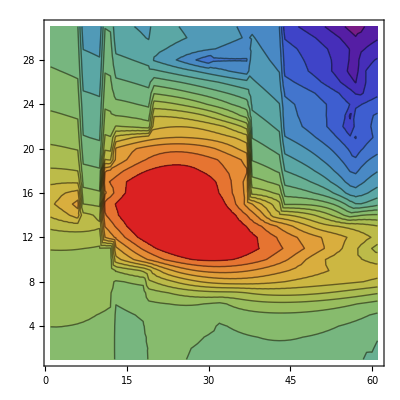

```mathematica
ListContourPlot[Transpose[downtoup],ColorFunction->"Rainbow",Contours->20]
```

```mathematica
Export["check.csv",downtoup];
```